increasing accuracy automatically
Note:
- We fixed the value of x at the reference point.
- We realized the 10^-137.

```mathematica
inittime=AbsoluteTime[];

Clear[W,K,v,V,t,x,T,X];
Clear[w0,A,a,B,b,Λ];
Clear[Kmat,Kinv];

Clear[zero];
zero[x_]=0;

W=w0-A Exp[-a T]+B  X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};


Clear[valA,vala,valB,valw0,ac];
V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
valA=1;
vala=4Pi^2;
valB=Exp[-4Pi^2];
veqntemp=V/.ReX->Sqrt[3]-1;
vteqntemp=FullSimplify@ComplexExpand[D[veqntemp,ReT]];
ac=1;
doinit=2.10;

list={{"accuracy","w_0","<T>","V|_0"}};

cnt=0;

While[ac<=100,
ac=ac+1;
Do[
cnt=cnt+1;
valw0=SetPrecision[(doinit+j*10^(-ac))*10^(-18),ac+10];
veqn=veqntemp*10^(46)/.{A->valA,a->vala,B->valB,w0->valw0};
vteqn=vteqntemp/.{A->valA,a->vala,B->valB,w0->valw0};
solvteq=NSolve[vteqn==0,{ReT},Reals,WorkingPrecision->10000];
Clear[relist];
relist={};
Do[
ret=ReT/.solvteq[[i]];
If[ret>0,
relist=Append[relist,ret];,relist=Append[relist,Null]];
,{i,1,Length[solvteq]}];
relist=DeleteCases[relist,Null];
minv=Min[Table[veqn/.ReT->relist[[k]],{k,1,Length[relist]}]];
If[minv<0,Break[];];
listveqn=Table[veqn/.ReT->relist[[k]],{k,1,Length[relist]}];
minvtrue=Min[listveqn];
ret=relist[[Position[listveqn,minvtrue][[1]]]];
,{j,0,10,1}];

doinit=valw0*10^(18)-10^(-ac);
list=Append[list,{ac,doinit*10^(-18),ret,minvtrue*10^(-46)}]
];

Print[N[list]//MatrixForm];
aclist=Table[list[[i,1]],{i,2,Length[list]}];
vminloglist=Table[Log10[list[[i,4]]*10^(-46)],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vminloglist[[k]]},{k,1,Length[list]-1}]]];

Print["time: ",AbsoluteTime[]-inittime];
```

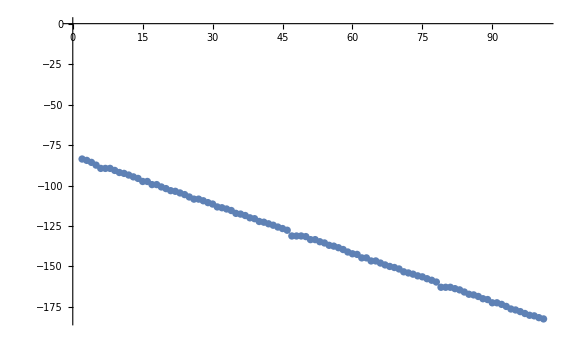
("accuracy" | "w_0" | "<T>" | "V|_0"
2. | 2.16×10^-18 | 1.17457 | 2.33923×10^-38
3. | 2.165×10^-18 | 1.17457 | 3.40413×10^-39
4. | 2.1658×10^-18 | 1.17457 | 2.04061×10^-40
5. | 2.16585×10^-18 | 1.17457 | 4.03858×10^-42
6. | 2.16585×10^-18 | 1.17457 | 3.81155×10^-44
7. | 2.16585×10^-18 | 1.17457 | 3.81155×10^-44
8. | 2.16585×10^-18 | 1.17457 | 3.81155×10^-44
9. | 2.16585×10^-18 | 1.17457 | 2.11127×10^-45
10. | 2.16585×10^-18 | 1.17457 | 1.11037×10^-46
11. | 2.16585×10^-18 | 1.17457 | 3.1028×10^-47
12. | 2.16585×10^-18 | 1.17457 | 3.02468×10^-48
13. | 2.16585×10^-18 | 1.17457 | 2.2435×10^-49
14. | 2.16585×10^-18 | 1.17457 | 2.43266×10^-50
15. | 2.16585×10^-18 | 1.17457 | 3.23771×10^-52
16. | 2.16585×10^-18 | 1.17457 | 3.23771×10^-52
17. | 2.16585×10^-18 | 1.17457 | 3.7331×10^-54
18. | 2.16585×10^-18 | 1.17457 | 3.7331×10^-54
19. | 2.16585×10^-18 | 1.17457 | 1.32682×10^-55
20. | 2.16585×10^-18 | 1.17457 | 1.2668×10^-56
21. | 2.16585×10^-18 | 1.17457 | 6.66562×10^-58
22. | 2.16585×10^-18 | 1.17457 | 2.66515×10^-58
23. | 2.16585×10^-18 | 1.17457 | 2.64871×10^-59
24. | 2.16585×10^-18 | 1.17457 | 2.48428×10^-60
25. | 2.16585×10^-18 | 1.17457 | 8.39975×10^-62
26. | 2.16585×10^-18 | 1.17457 | 3.98813×10^-63
27. | 2.16585×10^-18 | 1.17457 | 3.98813×10^-63
28. | 2.16585×10^-18 | 1.17457 | 3.87705×10^-64
29. | 2.16585×10^-18 | 1.17457 | 2.76624×10^-65
30. | 2.16585×10^-18 | 1.17457 | 3.6596×10^-66
31. | 2.16585×10^-18 | 1.17457 | 5.91732×10^-68
32. | 2.16585×10^-18 | 1.17457 | 1.91685×10^-68
33. | 2.16585×10^-18 | 1.17457 | 3.16666×10^-69
34. | 2.16585×10^-18 | 1.17457 | 3.66334×10^-70
35. | 2.16585×10^-18 | 1.17457 | 6.292×10^-72
36. | 2.16585×10^-18 | 1.17457 | 2.29153×10^-72
37. | 2.16585×10^-18 | 1.17457 | 2.91296×10^-73
38. | 2.16585×10^-18 | 1.17457 | 1.12636×10^-74
39. | 2.16585×10^-18 | 1.17457 | 3.26269×10^-75
40. | 2.16585×10^-18 | 1.17457 | 6.231×10^-77
41. | 2.16585×10^-18 | 1.17457 | 2.23053×10^-77
42. | 2.16585×10^-18 | 1.17457 | 2.30291×10^-78
43. | 2.16585×10^-18 | 1.17457 | 3.02676×10^-79
44. | 2.16585×10^-18 | 1.17457 | 2.26427×10^-80
45. | 2.16585×10^-18 | 1.17457 | 2.64038×10^-81
46. | 2.16585×10^-18 | 1.17457 | 2.40097×10^-82
47. | 2.16585×10^-18 | 1.17457 | 6.83873×10^-86
48. | 2.16585×10^-18 | 1.17457 | 6.83873×10^-86
49. | 2.16585×10^-18 | 1.17457 | 6.83873×10^-86
50. | 2.16585×10^-18 | 1.17457 | 2.83826×10^-86
51. | 2.16585×10^-18 | 1.17457 | 3.7936×10^-88
52. | 2.16585×10^-18 | 1.17457 | 3.7936×10^-88
53. | 2.16585×10^-18 | 1.17457 | 1.93182×10^-89
54. | 2.16585×10^-18 | 1.17457 | 3.31628×10^-90
55. | 2.16585×10^-18 | 1.17457 | 1.15902×10^-91
56. | 2.16585×10^-18 | 1.17457 | 3.58929×10^-92
57. | 2.16585×10^-18 | 1.17457 | 3.88914×10^-93
58. | 2.16585×10^-18 | 1.17457 | 2.88716×10^-94
59. | 2.16585×10^-18 | 1.17457 | 8.68304×10^-96
60. | 2.16585×10^-18 | 1.17457 | 6.82105×10^-97
61. | 2.16585×10^-18 | 1.17457 | 2.82058×10^-97
62. | 2.16585×10^-18 | 1.17457 | 2.02553×10^-99
63. | 2.16585×10^-18 | 1.17457 | 2.02553×10^-99
64. | 2.16585×10^-18 | 1.17457 | 2.52933×10^-101
65. | 2.16585×10^-18 | 1.17457 | 2.52933×10^-101
66. | 2.16585×10^-18 | 1.17457 | 1.29044×10^-102
67. | 2.16585×10^-18 | 1.17457 | 9.02956×10^-104
68. | 2.16585×10^-18 | 1.17457 | 1.02862×10^-104
69. | 2.16585×10^-18 | 1.17457 | 2.28524×10^-105
70. | 2.16585×10^-18 | 1.17457 | 2.85009×10^-106
71. | 2.16585×10^-18 | 1.17457 | 4.97645×10^-108
72. | 2.16585×10^-18 | 1.17457 | 9.75985×10^-109
73. | 2.16585×10^-18 | 1.17457 | 1.75891×10^-109
74. | 2.16585×10^-18 | 1.17457 | 1.58723×10^-110
75. | 2.16585×10^-18 | 1.17457 | 3.87086×10^-111
76. | 2.16585×10^-18 | 1.17457 | 2.70433×10^-112
77. | 2.16585×10^-18 | 1.17457 | 3.0405×10^-113
78. | 2.16585×10^-18 | 1.17457 | 2.40168×10^-114
79. | 2.16585×10^-18 | 1.17457 | 1.39383×10^-117
80. | 2.16585×10^-18 | 1.17457 | 1.39383×10^-117
81. | 2.16585×10^-18 | 1.17457 | 1.39383×10^-117
82. | 2.16585×10^-18 | 1.17457 | 1.9369×10^-118
83. | 2.16585×10^-18 | 1.17457 | 3.36709×10^-119
84. | 2.16585×10^-18 | 1.17457 | 1.66711×10^-120
85. | 2.16585×10^-18 | 1.17457 | 6.69242×10^-122
86. | 2.16585×10^-18 | 1.17457 | 2.69195×10^-122
87. | 2.16585×10^-18 | 1.17457 | 2.9167×10^-123
88. | 2.16585×10^-18 | 1.17457 | 1.16372×10^-124
89. | 2.16585×10^-18 | 1.17457 | 3.63623×10^-125
90. | 2.16585×10^-18 | 1.17457 | 3.58095×10^-127
91. | 2.16585×10^-18 | 1.17457 | 3.58095×10^-127
92. | 2.16585×10^-18 | 1.17457 | 3.80578×10^-128
93. | 2.16585×10^-18 | 1.17457 | 2.05353×10^-129
94. | 2.16585×10^-18 | 1.17457 | 5.32933×10^-131
95. | 2.16585×10^-18 | 1.17457 | 1.32886×10^-131
96. | 2.16585×10^-18 | 1.17457 | 1.28719×10^-132
97. | 2.16585×10^-18 | 1.17457 | 8.70494×10^-134
98. | 2.16585×10^-18 | 1.17457 | 7.03999×10^-135
99. | 2.16585×10^-18 | 1.17457 | 3.03952×10^-135
100. | 2.16585×10^-18 | 1.17457 | 2.3919×10^-136
101. | 2.16585×10^-18 | 1.17457 | 3.91666×10^-137)
-Graphics-

Evaluate both T & X

```mathematica
ClearAll;

inittime=AbsoluteTime[];

zero[x_]=0;

W=w0-A Exp[-a T]+B  X;
W̄=W/.{T->T̄,X->X̄};
K=-3Log[T+T̄]+X*X̄;

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, X]=D[W,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[W, TT]=D[W,{T,2}]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X]=D[K,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄]=D[K,X̄]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, TT]=D[K,{T,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ T̄]=D[K,{T̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, XX]=D[K,{X,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X̄ X̄]=D[K,{X̄,2}]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, TX]=D[K,T,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T X̄]=D[K,T,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X T̄]=D[K,T̄,X]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄ X̄]=D[K,T̄,X̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, X X̄]=D[K,X,X̄]/.{OverBar'->zero,OverBar''->zero};

DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T,X->X̄,X̄->X};
DXW=Subscript[W, X]+Subscript[K, X]*W;
OverBar[DXW]=DXW/.{T->T̄,T̄->T,X->X̄,X̄->X};

Kmat={{Subscript[K, T T̄],Subscript[K, T X̄]},{Subscript[K, X T̄],Subscript[K, X X̄]}};
Kinv=Inverse[Kmat];
Subscript[invK, T T̄]=Kinv[[1,1]];
Subscript[invK, T X̄]=Kinv[[1,2]];
Subscript[invK, X T̄]=Kinv[[2,1]];
Subscript[invK, X X̄]=Kinv[[2,2]];

vtemp=Exp[K]*(Subscript[invK, T T̄]*(DTW)*(OverBar[DTW])+Subscript[invK, T X̄]*(DTW)*(OverBar[DXW])+Subscript[invK, X T̄]*(DXW)*(OverBar[DTW])+Subscript[invK, X X̄]*(DXW)*(OverBar[DXW])-3W*W̄);
vxtemp=D[vtemp,X]/.{OverBar'->zero,OverBar''->zero};
vttemp=D[vtemp,T]/.{OverBar'->zero,OverBar''->zero};Clear[valA,vala,valB,valw0];

V=FullSimplify[ComplexExpand[vtemp/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
vxeqn=FullSimplify[ComplexExpand[D[V,ReX]]];
vteqn=FullSimplify[ComplexExpand[D[V,ReT]]];
dtweqn=FullSimplify[ComplexExpand[DTW/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
fteqn=FullSimplify[ComplexExpand[-Exp[K/2](Subscript[invK, T T̄]*(OverBar[DTW])+Subscript[invK, T X̄]*(OverBar[DXW]))/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
fxeqn=FullSimplify[ComplexExpand[-Exp[K/2](Subscript[invK, X T̄]*(OverBar[DTW])+Subscript[invK, X X̄]*(OverBar[DXW]))/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
mteqn=FullSimplify[ComplexExpand[-Exp[K/2]*Subscript[invK, T T̄]*Subscript[W, TT]/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];
m32eqn=FullSimplify[ComplexExpand[Exp[K/2]*W/.{T->ReT,T̄->ReT,X->ReX,X̄->ReX}]];

Block[{$MaxExtraPrecision=∞},

valA=1;
vala=4Pi^2;
valB=Exp[-4Pi^2];
veqntemp=V;

ac=1;
vorder=60;
doinit=2.10;

ret=1.0;rex=0.7;

list={{"accuracy","w_0","<T>","<X>","V|_0","V_T|_0","V_X|_0","D_TW|_0","F^T","F^X","m_T","m_(3/2)"}};

cnt=0;

While[ac<=69,
ac=ac+1;
Do[
cnt=cnt+1;
valw0=SetPrecision[(doinit+j*10^(-ac))*10^(-18),ac*2];
veqn=veqntemp*10^(vorder)/.{A->valA,a->vala,B->valB,w0->valw0};

Quiet[
solmin=FindMinimum[veqn,{{ReT,ret},{ReX,rex}},PrecisionGoal->100,AccuracyGoal->100,WorkingPrecision->5000,MaxIterations->1000,Method->"InteriorPoint"];
];

minv=solmin[[1]];
If[minv<=0,Break[]];
minvtrue=solmin[[1]];

,{j,0,10,1}];

ret=ReT/.solmin[[2]];
rex=ReX/.solmin[[2]];

doinit=valw0*10^(18)-10^(-ac);

valvt=vteqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};
valvx=vxeqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};
valdtw=dtweqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};
valft=fteqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};
valfx=fxeqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};
valmt=mteqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};
valm32=m32eqn/.{A->valA,a->vala,B->valB,w0->doinit*10^(-18)}/.{ReT->ret,ReX->rex};

list=Append[list,{ac,doinit*10^(-18),ret,rex,minvtrue*10^(-vorder),valvt,valvx,valdtw,valft,valvx,valmt,valm32}];
];
];

aclist=Table[list[[i,1]],{i,2,Length[list]}];

tlist=Table[list[[i,3]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],tlist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","<T>"}]];

vminloglist=Table[Log10[list[[i,5]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vminloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10V|_0"}]];

vtloglist=Table[Log10[Abs[list[[i,6]]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],vtloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10V_T|_0"}]];

dtwloglist=Table[Log10[Abs[list[[i,8]]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],dtwloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10D_TW|_0"}]];

ftloglist=Table[Log10[list[[i,9]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],ftloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10F^T|_0"}]];

mtloglist=Table[Log10[list[[i,11]]],{i,2,Length[list]}];
Print[ListPlot[Table[{aclist[[k]],mtloglist[[k]]},{k,1,Length[list]-1}],AxesLabel->{"accuracy","log_10m_T|_0"}]];

Print["w_0=",list[[Length[list],2]]];
Print["<T>=",N[list[[Length[list],3]],10]];
Print["<X>=",N[list[[Length[list],4]],10]];
Print["V|_0=",N[list[[Length[list],5]],10]];

Print[N[list,4]//MatrixForm];

time=AbsoluteTime[]-inittime;
hour=Floor[time/3600];
min=Floor[(time-hour*3600)/60];
sec=Floor[time-hour*3600-min*60];
Print["time: ",hour,"時間",min,"分",sec,"秒"];
```

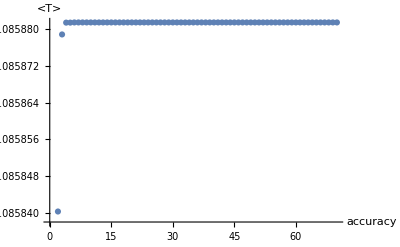
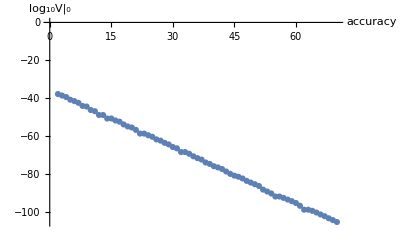
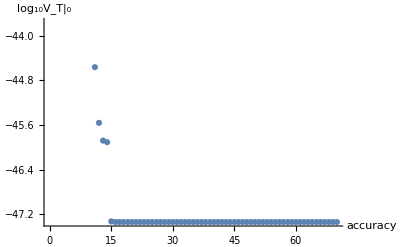
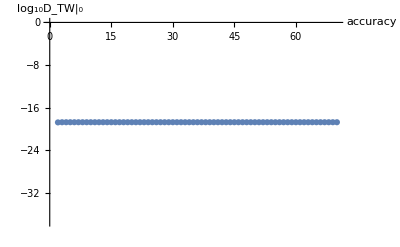
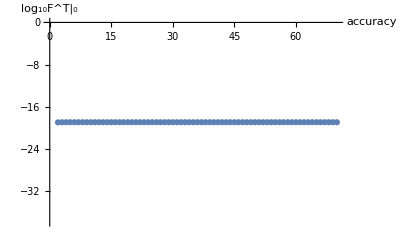
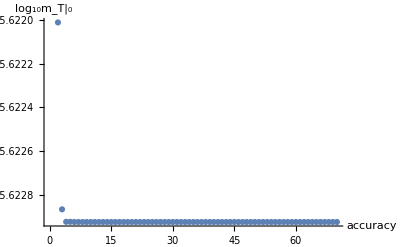
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
"w_0="2.1635936819130304481419179838664985466317039138179583995186330956864175452853638532363075193362571342407564045235072239892560987332665368287×10^-18
"<T>="1.085881478
"<X>="0.7142953447
"V|_0="3.20022422×10^-106
("accuracy" | "w_0" | "<T>" | "<X>" | "V|_0" | "V_T|_0" | "V_X|_0" | "D_TW|_0" | "F^T" | "F^X" | "m_T" | "m_(3/2)"
2. | 2.16×10^-18 | 1.086 | 0.715 | 1.39848×10^-38 | -3.×10^-36 | -1.×10^-38 | -1.8×10^-19 | 1.2×10^-19 | -1.×10^-38 | 2.388×10^-16 | 2.839×10^-18
3. | 2.163×10^-18 | 1.086 | 0.7143 | 2.312×10^-39 | -2.7×10^-37 | -1.×10^-39 | -1.961×10^-19 | 1.244×10^-19 | -1.×10^-39 | 2.383×10^-16 | 2.837×10^-18
4. | 2.164×10^-18 | 1.086 | 0.7143 | 3.648×10^-40 | -2.72×10^-38 | -1.2×10^-40 | -1.974×10^-19 | 1.251×10^-19 | -1.2×10^-40 | 2.383×10^-16 | 2.837×10^-18
5. | 2.164×10^-18 | 1.086 | 0.7143 | 1.434×10^-41 | -2.716×10^-39 | -1.22×10^-41 | -1.975×10^-19 | 1.252×10^-19 | -1.22×10^-41 | 2.383×10^-16 | 2.837×10^-18
6. | 2.164×10^-18 | 1.086 | 0.7143 | 2.655×10^-42 | -2.716×10^-40 | -1.221×10^-42 | -1.975×10^-19 | 1.252×10^-19 | -1.221×10^-42 | 2.383×10^-16 | 2.837×10^-18
7. | 2.164×10^-18 | 1.086 | 0.7143 | 3.19×10^-43 | -2.716×10^-41 | -1.221×10^-43 | -1.975×10^-19 | 1.252×10^-19 | -1.221×10^-43 | 2.383×10^-16 | 2.837×10^-18
8. | 2.164×10^-18 | 1.086 | 0.7143 | 7.45×10^-45 | -2.716×10^-42 | -1.221×10^-44 | -1.975×10^-19 | 1.252×10^-19 | -1.221×10^-44 | 2.383×10^-16 | 2.837×10^-18
9. | 2.164×10^-18 | 1.086 | 0.7143 | 3.555×10^-45 | -2.716×10^-43 | -1.22×10^-45 | -1.975×10^-19 | 1.252×10^-19 | -1.22×10^-45 | 2.383×10^-16 | 2.837×10^-18
10. | 2.164×10^-18 | 1.086 | 0.7143 | 5.074×10^-47 | -2.715×10^-44 | -1.219×10^-46 | -1.975×10^-19 | 1.252×10^-19 | -1.219×10^-46 | 2.383×10^-16 | 2.837×10^-18
11. | 2.164×10^-18 | 1.086 | 0.7143 | 1.18×10^-47 | -2.716×10^-45 | -1.224×10^-47 | -1.975×10^-19 | 1.252×10^-19 | -1.224×10^-47 | 2.383×10^-16 | 2.837×10^-18
12. | 2.164×10^-18 | 1.086 | 0.7143 | 1.185×10^-49 | -2.739×10^-46 | -1.308×10^-48 | -1.975×10^-19 | 1.252×10^-19 | -1.308×10^-48 | 2.383×10^-16 | 2.837×10^-18
13. | 2.164×10^-18 | 1.086 | 0.7143 | 1.185×10^-49 | -1.315×10^-46 | -5.618×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -5.618×10^-49 | 2.383×10^-16 | 2.837×10^-18
14. | 2.164×10^-18 | 1.086 | 0.7143 | 1.711×10^-51 | -1.233×10^-46 | -5.252×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -5.252×10^-49 | 2.383×10^-16 | 2.837×10^-18
15. | 2.164×10^-18 | 1.086 | 0.7143 | 1.711×10^-51 | -4.71×10^-48 | -1.435×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.435×10^-49 | 2.383×10^-16 | 2.837×10^-18
16. | 2.164×10^-18 | 1.086 | 0.7143 | 1.531×10^-52 | -4.602×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
17. | 2.164×10^-18 | 1.086 | 0.7143 | 3.632×10^-53 | -4.594×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
18. | 2.164×10^-18 | 1.086 | 0.7143 | 1.275×10^-54 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
19. | 2.164×10^-18 | 1.086 | 0.7143 | 1.067×10^-55 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
20. | 2.164×10^-18 | 1.086 | 0.7143 | 2.883×10^-56 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
21. | 2.164×10^-18 | 1.086 | 0.7143 | 1.576×10^-57 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
22. | 2.164×10^-18 | 1.086 | 0.7143 | 1.789×10^-59 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
23. | 2.164×10^-18 | 1.086 | 0.7143 | 1.789×10^-59 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
24. | 2.164×10^-18 | 1.086 | 0.7143 | 2.313×10^-60 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
25. | 2.164×10^-18 | 1.086 | 0.7143 | 3.655×10^-61 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
26. | 2.164×10^-18 | 1.086 | 0.7143 | 1.502×10^-62 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
27. | 2.164×10^-18 | 1.086 | 0.7143 | 3.343×10^-63 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
28. | 2.164×10^-18 | 1.086 | 0.7143 | 2.273×10^-64 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
29. | 2.164×10^-18 | 1.086 | 0.7143 | 3.26×10^-65 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
30. | 2.164×10^-18 | 1.086 | 0.7143 | 1.444×10^-66 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
31. | 2.164×10^-18 | 1.086 | 0.7143 | 2.757×10^-67 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
32. | 2.164×10^-18 | 1.086 | 0.7143 | 3.094×10^-69 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
33. | 2.164×10^-18 | 1.086 | 0.7143 | 3.094×10^-69 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
34. | 2.164×10^-18 | 1.086 | 0.7143 | 3.679×10^-70 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
35. | 2.164×10^-18 | 1.086 | 0.7143 | 1.746×10^-71 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
36. | 2.164×10^-18 | 1.086 | 0.7143 | 1.879×10^-72 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
37. | 2.164×10^-18 | 1.086 | 0.7143 | 3.21×10^-73 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
38. | 2.164×10^-18 | 1.086 | 0.7143 | 9.446×10^-75 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
39. | 2.164×10^-18 | 1.086 | 0.7143 | 1.658×10^-75 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
40. | 2.164×10^-18 | 1.086 | 0.7143 | 1.006×10^-76 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
41. | 2.164×10^-18 | 1.086 | 0.7143 | 2.275×10^-77 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
42. | 2.164×10^-18 | 1.086 | 0.7143 | 3.28×10^-78 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
43. | 2.164×10^-18 | 1.086 | 0.7143 | 1.646×10^-79 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
44. | 2.164×10^-18 | 1.086 | 0.7143 | 8.834×10^-81 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
45. | 2.164×10^-18 | 1.086 | 0.7143 | 1.045×10^-81 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
46. | 2.164×10^-18 | 1.086 | 0.7143 | 2.666×10^-82 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
47. | 2.164×10^-18 | 1.086 | 0.7143 | 3.294×10^-83 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
48. | 2.164×10^-18 | 1.086 | 0.7143 | 1.783×10^-84 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
49. | 2.164×10^-18 | 1.086 | 0.7143 | 2.255×10^-85 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
50. | 2.164×10^-18 | 1.086 | 0.7143 | 3.081×10^-86 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
51. | 2.164×10^-18 | 1.086 | 0.7143 | 3.548×10^-87 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
52. | 2.164×10^-18 | 1.086 | 0.7143 | 4.323×10^-89 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
53. | 2.164×10^-18 | 1.086 | 0.7143 | 4.293×10^-90 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
54. | 2.164×10^-18 | 1.086 | 0.7143 | 3.99×10^-91 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
55. | 2.164×10^-18 | 1.086 | 0.7143 | 9.575×10^-93 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
56. | 2.164×10^-18 | 1.086 | 0.7143 | 9.575×10^-93 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
57. | 2.164×10^-18 | 1.086 | 0.7143 | 1.787×10^-93 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
58. | 2.164×10^-18 | 1.086 | 0.7143 | 2.295×10^-94 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
59. | 2.164×10^-18 | 1.086 | 0.7143 | 3.478×10^-95 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
60. | 2.164×10^-18 | 1.086 | 0.7143 | 3.623×10^-96 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
61. | 2.164×10^-18 | 1.086 | 0.7143 | 1.179×10^-97 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
62. | 2.164×10^-18 | 1.086 | 0.7143 | 1.047×10^-99 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
63. | 2.164×10^-18 | 1.086 | 0.7143 | 1.047×10^-99 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
64. | 2.164×10^-18 | 1.086 | 0.7143 | 2.679×10^-100 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
65. | 2.164×10^-18 | 1.086 | 0.7143 | 3.426×10^-101 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
66. | 2.164×10^-18 | 1.086 | 0.7143 | 3.107×10^-102 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
67. | 2.164×10^-18 | 1.086 | 0.7143 | 3.812×10^-103 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
68. | 2.164×10^-18 | 1.086 | 0.7143 | 3.069×10^-104 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
69. | 2.164×10^-18 | 1.086 | 0.7143 | 3.435×10^-105 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18
70. | 2.164×10^-18 | 1.086 | 0.7143 | 3.2×10^-106 | -4.591×10^-48 | -1.43×10^-49 | -1.975×10^-19 | 1.252×10^-19 | -1.43×10^-49 | 2.383×10^-16 | 2.837×10^-18)
"time: "0"時間"17"分"3"秒"

```mathematica
inittime=AbsoluteTime[];

tmin=1.0856;
tmax=1.0861;
xmin=0.708;
xmax=0.720;
vmin=2.000;
vmax=3.000;

valA=1;
vala=4Pi^2;
valB=Exp[-4Pi^2];
valw0=2.163*10^(-18);

Print[Plot3D[veqntemp*10^(39)/.{A->valA,a->vala,B->valB,w0->valw0},{ReT,tmin,tmax},{ReX,xmin,xmax},PlotRange->{{tmin,tmax},{xmin,xmax},{vmin,vmax}},PlotPoints->100,WorkingPrecision->2000,AxesLabel->{"ReT","ReX","V×10^39"}]];

Print[Plot3D[vteqn*10^(40)/.{A->valA,a->vala,B->valB,w0->valw0},{ReT,tmin,tmax},{ReX,xmin,xmax},PlotRange->{{tmin,tmax},{xmin,xmax},{-1,1}},PlotPoints->100,WorkingPrecision->2000,AxesLabel->{"ReT","ReX","V_T×10^40"}]];

Print[Plot3D[vxeqn*10^(40)/.{A->valA,a->vala,B->valB,w0->valw0},{ReT,tmin,tmax},{ReX,xmin,xmax},PlotRange->{{tmin,tmax},{xmin,xmax},{-1,1}},PlotPoints->100,WorkingPrecision->2000,AxesLabel->{"ReT","ReX","V_X×10^40"}]];

(*実際に極致を求めようとするが・・・*)
(*Block[{$MaxExtraPrecision},
vt=vteqn*10^(50)/.{A->valA,a->vala,B->valB,w0->valw0};
vx=vxeqn*10^(50)/.{A->valA,a->vala,B->valB,w0->valw0};
Print[NSolve[vt==0&&vx==0&&{ReT,ReX}∈Rectangle[{0,0},{3,3}],{ReT,ReX}]];
];*)

time=AbsoluteTime[]-inittime;
hour=Floor[time/3600];
min=Floor[(time-hour*3600)/60];
sec=Floor[time-hour*3600-min*60];
Print["time: ",hour,"時間",min,"分",sec,"秒"];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

time: 0時間0分26秒